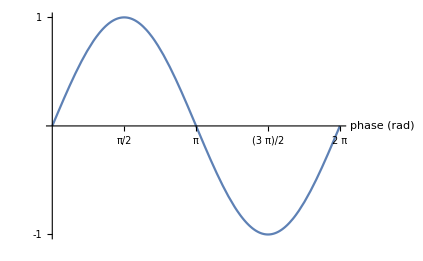

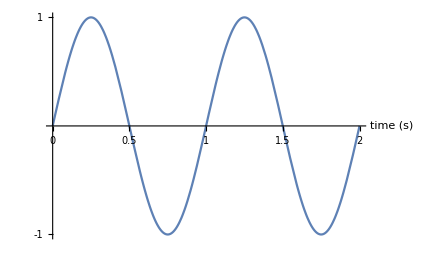

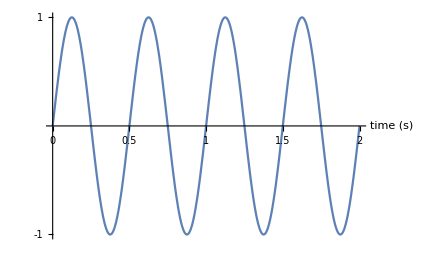

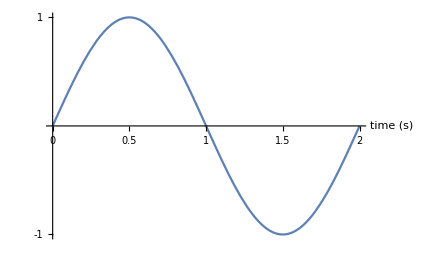

```mathematica
Plot[Sin[x],{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"phase (rad)", None},AxesStyle->Directive["Label", 16]]
Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
Plot[Sin[4π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
Plot[Sin[1π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
```

```mathematica
6.43*10^-4*80^2
```

4.1152

Lesson 2

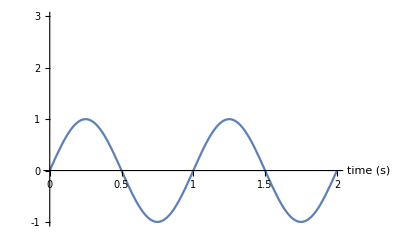

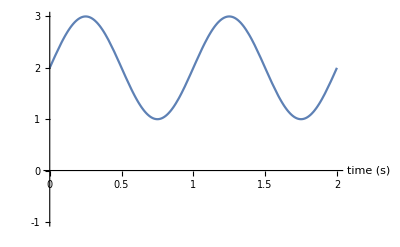

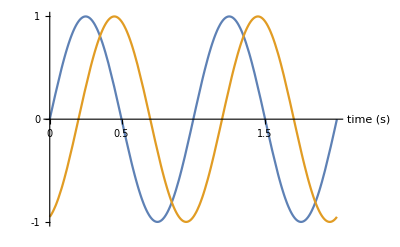

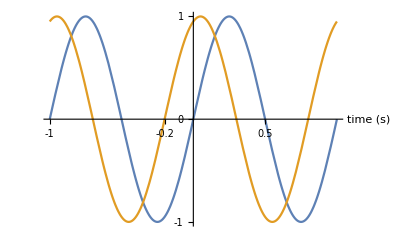

```mathematica
Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,0,1,2,3}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,3}]
Plot[2+Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,0,1,2,3}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,3}]
Plot[{Sin[2π t],Sin[2π (t-0.2)]},{t,0,2},Ticks->{{0,0.2,0.5,1,1.5,2},{-1,0,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,1}]
Plot[{Sin[2π t],Sin[2π (t+0.2)]},{t,-1,1},Ticks->{{-1,-0.5,-0.2,0,0.5,1,1.5,2},{-1,0,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,1}]
```

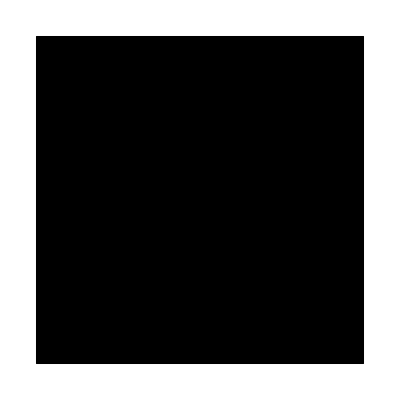

```mathematica
Graphics[{EdgeForm[{Thick, Black}],Rectangle[]}]
```

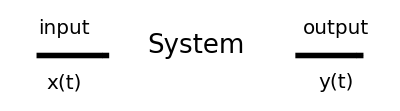

```mathematica
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["input",FontSize->20],{-5,8}],
Text[Style["x(t)",FontSize->20],{-5,2}],
Text[Style["output",FontSize->20],{25,8}],
Text[Style["y(t)",FontSize->20],{25,2}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
```

```mathematica
Graphics[{Style[Line[{{0,2},{0,-5}}], Thick,Dashed],
Line[{{0,0},{3,-3}}],
Circle[{0,0},1,{-π/2,-.8}],
Text[Style["y",FontSize->23],{0.5,-1.5}],
Disk[{3,-3},0.3]
}]
```

-Graphics-

```mathematica
Simplify[Sin[a]/Sin[b]]
```

Csc[b] Sin[a]

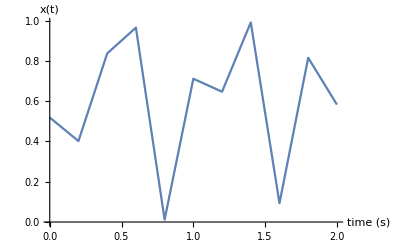

```mathematica
ListPlot[Table[{n,RandomReal[]},{n,0,2,0.2}],Joined->True,AxesLabel->{"time (s)","x(t)"},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
```

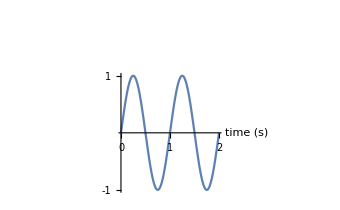

```mathematica
sinPlot=Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]];
Show[{Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]],
Graphics[{
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["input",FontSize->20],{-5,8}],
Text[Style["x(t)",FontSize->20],{-5,2}],
Text[Style["output",FontSize->20],{25,8}],
Text[Style["y(t)",FontSize->20],{25,2}],
Text[Style["System",FontSize->26],{9.5,6}]
}]}]
```

```mathematica
1^2/2^2
```

1/4

```mathematica
1/(1-1/3)
```

3/2

```mathematica
1/(1-1/4.)
1/(1-4/1.)
```

1.33333

-0.333333

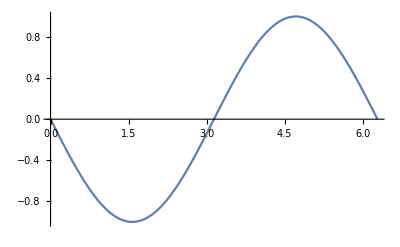

```mathematica
Plot[Sin[x-π],{x,0,2π}]
```

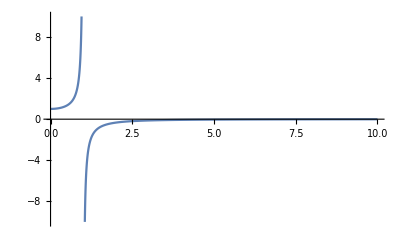

```mathematica
Plot[1/(1-w^2),{w,0,10},PlotRange->{-10,10}]
```

```mathematica
1/(1-1/9.)*0.2
```

0.225

```mathematica
Solve[1/(1-4/1.)*x==1]
```

{{x→-3.}}

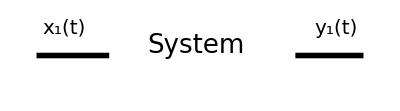

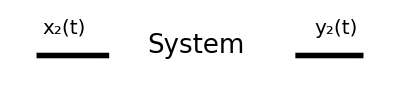

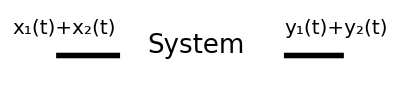

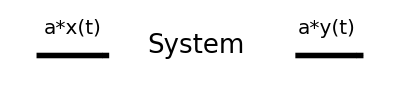

```mathematica
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["x_1(t)",FontSize->20],{-5,8}],
Text[Style["y_1(t)",FontSize->20],{25,8}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["x_2(t)",FontSize->20],{-5,8}],
Text[Style["y_2(t)",FontSize->20],{25,8}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["x_1(t)+x_2(t)",FontSize->20],{-7,8}],
Text[Style["y_1(t)+y_2(t)",FontSize->20],{27,8}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["a*x(t)",FontSize->20],{-4,8}],
Text[Style["a*y(t)",FontSize->20],{24,8}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
```

```mathematica
ω1=2;
ω2=0.5;
1/(1-ω1^2)*(-3)
1/(1-ω2^2)*0.75
```

1

1.

```mathematica
∑_j Subscript[A, jr] Subscript[A, js]
```

```mathematica
∫_0^(2π) Sin[ϕ]^2 ⅆϕ
```

π

```mathematica
∫_0^(2π) Sin[ϕ]Cos[ϕ]ⅆϕ
```

0

```mathematica
∫_(-π/2)^(π/2) Cos[θ]ⅆθ
```

2

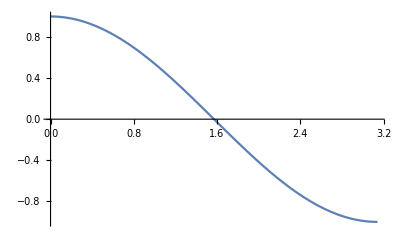

```mathematica
Plot[Cos[θ],{θ,0,π}]
```

```mathematica
∫_0^(2π) Sin[ϕ]^2 ⅆϕ
```

π

```mathematica
∫_0^(2π) Sin[ϕ]*Cos[ϕ]ⅆϕ
```

0

```mathematica
Eigensystem[({{2, 0, 0}, {0, 2, 0}, {0, 0, 4}})]
Eigenvalues[({{2, 0, 0}, {0, 2, 0}, {0, 0, 2}})]
```

{{4,2,2},{{0,0,1},{0,1,0},{1,0,0}}}

{2,2,2}

```mathematica
Sin[60°]*Cos[60°]
```

(√3)/4

```mathematica
(5*√3)/8.
```

1.08253

```mathematica
UnitConvert[12/(20*1.08*10^-8)hr,yr]
```

6341.96 yr

```mathematica
Unprotect[q]
Clear[q]
```

{q}

```mathematica
q[Q_,P_]:=√(2*P)Sin[Q]
p[Q_,P_]:=√(2*P)Cos[Q]
```

```mathematica
D[q[Q,P], Q]
D[q[Q,P], P]
```

√2 √P Cos[Q]

Sin[Q]/(√2 √P)

```mathematica
1/Cos[40°]*12.
```

15.6649